```mathematica
h=MakeInnerOuterGraph[{2,2,2,2,2}]
```

{1<->2,2<->3,3<->4,4<->5,5<->1,6<->1,6<->5,7<->1,7<->6,8<->1,8<->7,9<->2,9<->8,9<->1,10<->2,10<->9,11<->2,11<->10,12<->3,12<->11,12<->2,13<->3,13<->12,14<->3,14<->13,15<->4,15<->14,15<->3,16<->4,16<->15,17<->4,17<->16,18<->5,18<->17,18<->4,19<->5,19<->18,20<->5,20<->19,20<->6}

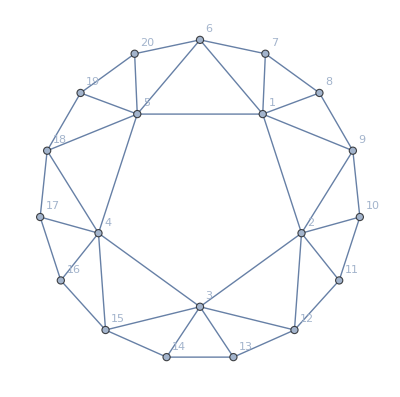

```mathematica
Graph[h,VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

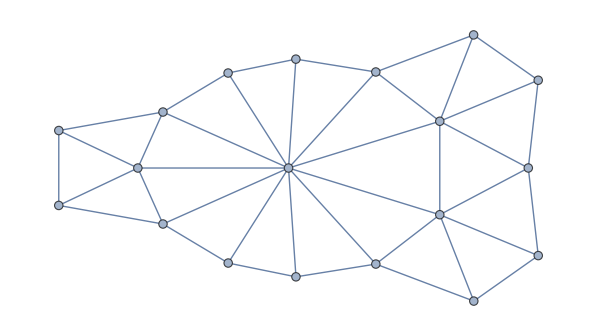

```mathematica
g=Graph[VertexContract[Graph[h],{1,3}]]
```

```mathematica
pos=GraphEmbedding[g,"TutteEmbedding"]
```

{{0.712199,-0.231408},{-0.610459,-0.117232},{-0.424965,0.453658},{-1.83697×10^-16,1.},{0.406737,0.913545},{0.743145,0.669131},{0.951057,0.309017},{0.994522,-0.104528},{0.866025,-0.5},{0.587785,-0.809017},{0.207912,-0.978148},{-0.207912,-0.978148},{-0.587785,-0.809017},{-0.866025,-0.5},{-0.994522,-0.104528},{-0.951057,0.309017},{-0.743145,0.669131},{-0.406737,0.913545},{0.16161,-0.0525108}}

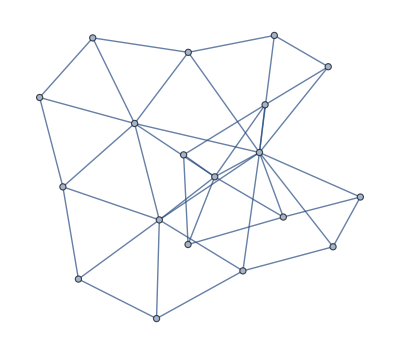

```mathematica
g2=EdgeAdd[g,{2<->5,2<->4}]
```

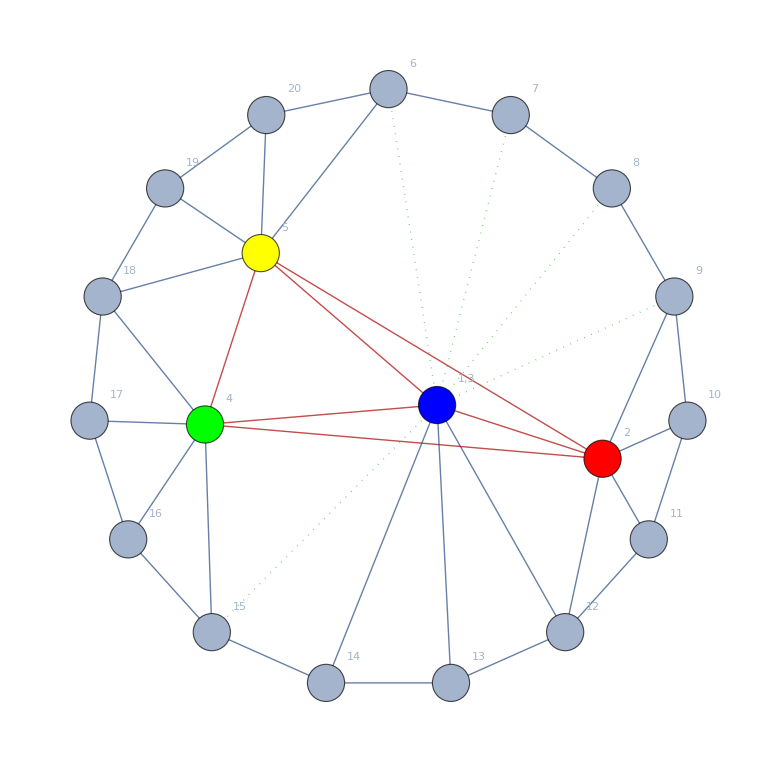

```mathematica
Graph[g2,VertexCoordinates->pos,VertexLabels->Join[{1->"1,3"},Table[i->i,{i,2,20}]],VertexStyle->{1 -> Blue, 2 -> Red,4->Green,5->Yellow},EdgeStyle->Join[
Table[e->{Thick,Darker[Red]},{e,{1<->2,1<->4,1<->5,2<->5,2<->4,4<->5}}],
Table[i<->1->{Thick,Dotted,Darker[Green]},{i,{6,7,8,9,10,11,15,16,17,18}}]],VertexSize->Large]
```

```mathematica
VertexList[Graph[MakeInnerOuterGraph[{0,1,2,3,4}]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
VertexLabels->Join[{1->"1,3"},Table[i->i,{i,2,20}]]
```

VertexLabels→{1→1,3,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10,11→11,12→12,13→13,14→14,15→15,16→16,17→17,18→18,19→19,20→20}

```mathematica
ChromaticPolynomial[g2,4]/24
```

4554

```mathematica
ChromaticPolynomial[GraphData["PetersenGraph"],4]/24
```

540